```mathematica
SetDirectory[NotebookDirectory[]<>"Simulation\\Simulation\\bin\\Release"]
```

```mathematica
data=BinaryReadList[".\\Data\\"<>RunProcess["Simulation.exe","StandardOutput"]<>"\\data.bin",ConstantArray["Real64",100]];
```

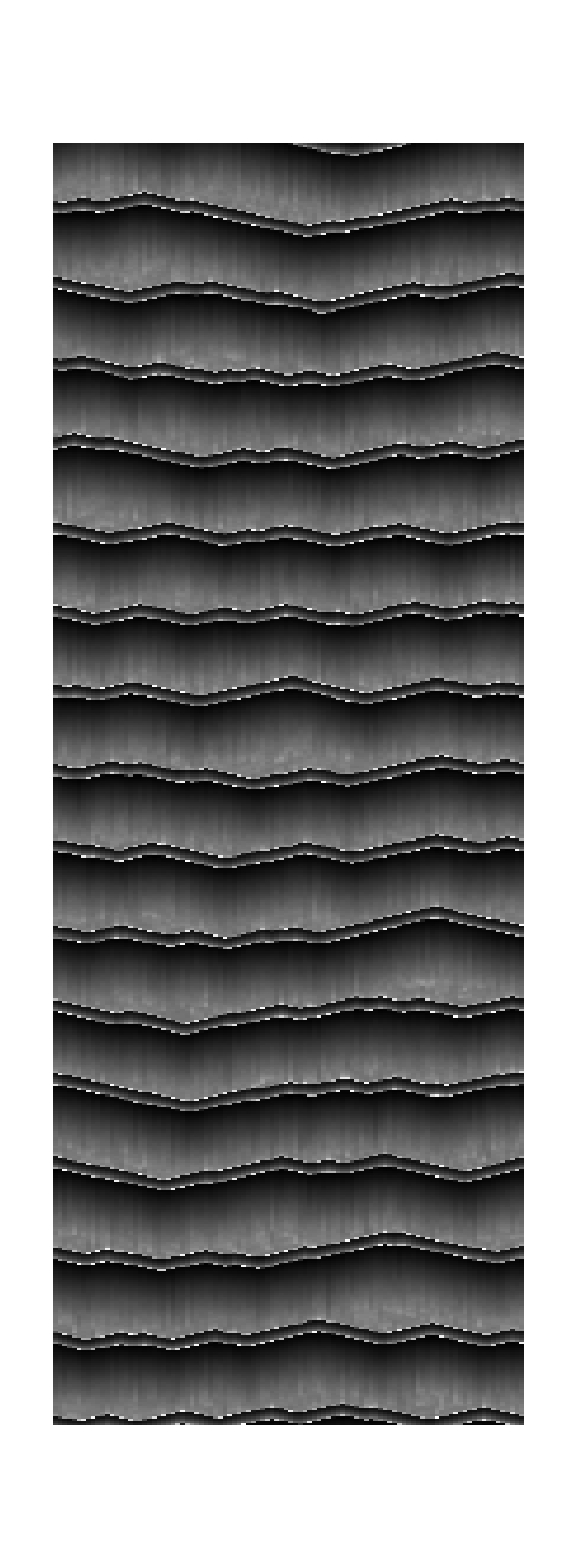

```mathematica
ArrayPlot[data]
```